```mathematica
Integrate[(1/2 a x^2+1/4 x^4)Exp[-1/2 a x^2-1/4 x^4],{x,-∞,∞}]/Integrate[Exp[-1/2 a x^2-1/4 x^4],{x,-∞,∞}]//Simplify
```

ConditionalExpression[1/8 (2-a^2+(a^2 BesselK[3/4,a^2/8])/BesselK[1/4,a^2/8]), Re[a]>0]

```mathematica
Integrate[(1/4 a^2+1/2 a x^2+1/4 x^4)Exp[-1/2 a x^2-1/4 x^4],{x,-∞,∞}]/Integrate[Exp[-1/2 a x^2-1/4 x^4],{x,-∞,∞}]//Simplify
```

ConditionalExpression[1/8 (2+a^2+(a^2 BesselK[3/4,a^2/8])/BesselK[1/4,a^2/8]), Re[a]>0]

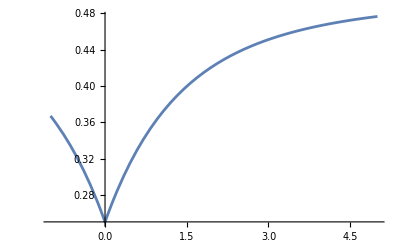

```mathematica
f=1/8 (2-a^2+(a^2 BesselK[3/4,a^2/8])/BesselK[1/4,a^2/8]);
Plot[f,{a,-1,5}]
```

```mathematica
https://dlmf.nist.gov/10.34
```

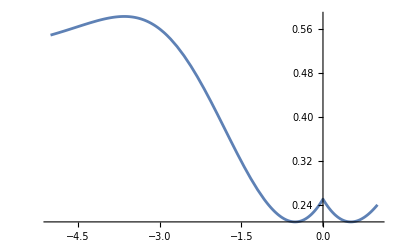

```mathematica
g=1/8 (2+a^2-(a^2 (BesselK[3/4,a^2/8]+Sqrt[2]π BesselI[3/4,a^2/8]))/(BesselK[1/4,a^2/8]+Sqrt[2]π BesselI[1/4,a^2/8]));
Plot[g,{a,-5,1}]
```

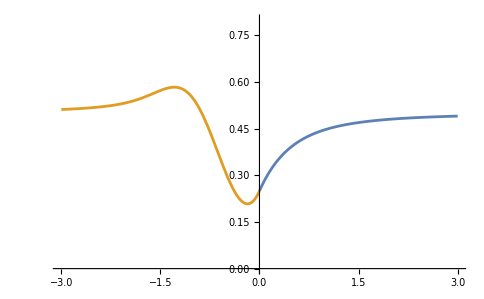

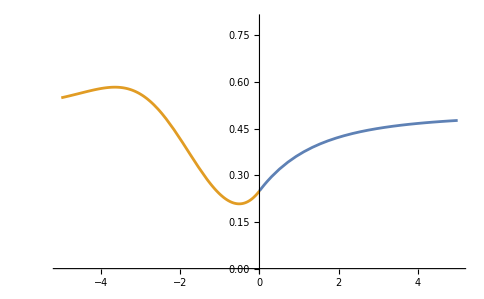

```mathematica
h={ConditionalExpression[f, Re[a]>0],ConditionalExpression[g, Re[a]<0]}/.{a->Sqrt[8]x};
Plot[h,{x,-3,3},PlotRange->{0,0.8}]
h={ConditionalExpression[f, Re[a]>0],ConditionalExpression[g, Re[a]<0]};
Plot[h,{a,-5,5},PlotRange->{0,0.8}]
```

```mathematica
Export["/Users/andrewgomes/Documents/LatticeFeatures/dof.png",%14,"PNG"]
```

/Users/andrewgomes/Documents/LatticeFeatures/dof.png

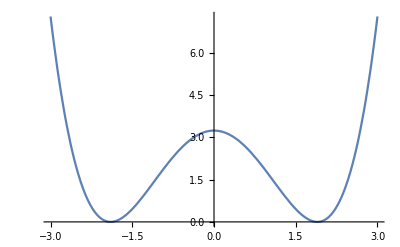

```mathematica
Plot[(1/4 a^2+1/2 a x^2+1/4 x^4)/.{a->-3.6},{x,-3,3}]
```